```mathematica
Remove["Global`*"]
```

```mathematica
γ=1/2;
Expγ[x_] := If[γ==0, Exp[x], (1+γ x)^(1/γ)];
Logγ[x_] := If[γ==0, Log[x], (x^γ-1)/γ];
```

```mathematica
Logγ[Expγ[y]] // PowerExpand // FullSimplify
```

y

```mathematica
Clear[CircleTimes];
CircleTimes[x_,y_] := FullSimplify[PowerExpand[Expγ[Logγ[x] + Logγ[y]]]];
```

```mathematica
X0 = 2;
x[t_, g_] := X0 ⊗ Expγ[Logγ[g] t];
```

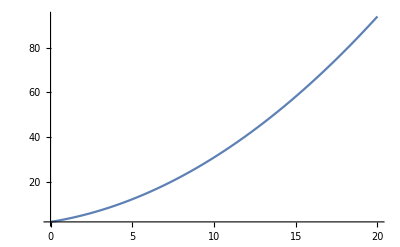

```mathematica
Plot[x[t,2], {t, 0, 20}, PlotRange->Full]
```

```mathematica
x[1,2]
```

9-4 √2